# Initialization

```mathematica
Block[{Print},<<xAct`xCoba`;]
Block[{Print},<<xAct`xPert`;]
<<KerrWithProca`

(*$PrePrint=ScreenDollarIndices; *)
Off[ValidateSymbol::used]
Off[ValidateSymbol::invalid]
$DefInfoQ=False;
$UndefInfoQ=False;
$CVSimplify=Together;
$Assumptions={r>0,0≤θ≤π, 0≤ϕ≤2*π,0≤a<1,m∈Integers, l∈NonNegativeIntegers, lp∈NonNegativeIntegers, μ≥0, ν∈Complexes, ω∈Complexes, ν≂̸0, ω≂̸0, 0≤χ<1};
(*Since were only using one covariant derivative, redefine printed symbols*)
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";

concise[expr_]:=Tooltip[●, expr]

SolutionPath = NotebookDirectory[]<>"Solutions/";
PlotPath = NotebookDirectory[]<>"Plots/";
LogFile = NotebookDirectory[]<>"RunLogs.txt";
PlotFileExtension = ".png";
If[¬DirectoryQ[SolutionPath],CreateDirectory[SolutionPath]]
If[¬DirectoryQ[PlotPath],CreateDirectory[PlotPath]]

PurgeSolutions[]:=
(DeleteDirectory[SolutionPath, DeleteContents->True];
CreateDirectory[SolutionPath];
)
```

# Setup manifold and associated objects

```mathematica
(*Define basic objects of xAct*)
DefManifold[ℳ,4, {μ,ν,α,β,ρ,σ,γ,δ}]; (*Manifold of our spacetime*)
DefChart[sphericalchart, ℳ,{0,1,2,3},{t[],r[],θ[],ϕ[]}, FormatBasis->{"Partials", "Differentials"}, ChartColor->Blue]; (*Spherical co-ordinate chart*)
(*Cast numerical indices to latin/greek representation*)
ch/:CIndexForm[0,ch]:="t";
ch/:CIndexForm[1,ch]:="r";
ch/:CIndexForm[2,ch]:="θ";
ch/:CIndexForm[3,ch]:="ϕ";

(*Define metric object*)
DefMetric[-1,g[-μ,-ν], CD, {";", "∇"},PrintAs->"g"]


(*Define the constants of the system*)
DefConstantSymbol[M] (*Mass of BH*)
DefConstantSymbol[J](*Angular momentum of BH*)
DefConstantSymbol[a](*Dimensionless spin*)
DefConstantSymbol[G](*Newtons constant*)
DefConstantSymbol[λ](*separation constant for polarization tensor*)
DefConstantSymbol[ω](*angular frequency*)
DefConstantSymbol[m](*projected angular momentum quantum number*)
DefConstantSymbol[Μ](*Mass of proca field*);
```

# Define the basic geometric objects and their components

```mathematica
(*Define the components of the metric. Note, the chart co-ordinates are scalar functions*)
KerrComponents = {{-1+(2 M r[])/((J^2 Cos[θ[]]^2)/M^2+r[]^2),0,0,-(2 J r[] Sin[θ[]]^2)/((J^2 Cos[θ[]]^2)/M^2+r[]^2)},{0,(J^2 Cos[θ[]]^2+M^2 r[]^2)/(J^2+M^2 r[] (-2 M+r[])),0,0},{0,0,(J^2 Cos[θ[]]^2)/M^2+r[]^2,0},{-(2 J r[] Sin[θ[]]^2)/((J^2 Cos[θ[]]^2)/M^2+r[]^2),0,0,Sin[θ[]]^2 (J^2/M^2+r[]^2+(2 J^2 M r[] Sin[θ[]]^2)/(J^2 Cos[θ[]]^2+M^2 r[]^2))}}/.J->a*M//FullSimplify;
SchwarComponents = {{-1+(2 M)/r[],0,0,0},{0,1/(1-(2 M)/r[]),0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}};

met = CTensor[KerrComponents, {-sphericalchart,-sphericalchart}];
SetCMetric[met,-sphericalchart,SignatureOfMetric->{3,1,0}];
g=met;
(*MetricInBasis[g,-sphericalchart,SchwarComponents]; (*Cast the components onto the metric object*)*)
MetricCompute[g,sphericalchart,All]; (*Precompute all metric-derived quantities, e.g. christoffel, riemann, etc.*)

(*represent the metric in a CTensor form*)
(met = ToCTensor[g,{-sphericalchart, -sphericalchart}]/.TensorValues[g])[-μ,-ν];

(*Define the covariant derivative of this CTensor metric*)
Cd = CovDOfMetric[met];
(*Define christoffel in CTensor repr.*)
christoffel = Head[ChristoffelFromMetric[met[-μ,-ν], sphericalchart][α,-β,-γ]//FromBasisExpand//Simplification];

(*Verify covariant derivative of metric vanishes*)
MetricCompatibleTest = (Cd[-μ][met[-μ,-ν]]==0);

(*Define the killing fields*)
Φ = CTensor[{0,0,0,1}, {sphericalchart}];
T = CTensor[{1,0,0,0}, {sphericalchart}];

IsometryTest = (LieD[T[{α,sphericalchart}],PDsphericalchart]@met[{-μ,-sphericalchart},{-ν,-sphericalchart}]==0)&&(LieD[Φ[{α,sphericalchart}],PDsphericalchart]@met[{-μ,-sphericalchart},{-ν,-sphericalchart}]==0);
If[¬(MetricCompatibleTest&&IsometryTest), Print["Test Failure!"]]
```

# Define the Proca vector field object and generate the symmetries induced by Kerr background

```mathematica
DefTensor[A[μ], ℳ]
sym1 = ContractBasis[LieD[Φ[α],PDsphericalchart]@A[μ]//ToBasis[sphericalchart], OverDerivatives->True]//Simplify;
sym2 = ContractBasis[LieD[T[α],PDsphericalchart]@A[μ]//ToBasis[sphericalchart], OverDerivatives->True]//Simplify;
procafieldsymmetry = {sym1,sym2};
```

# Define the Polarization tensor used in the FKKS ansatz

```mathematica
(*Define CTensor representation of the polarization tensor from the FKKS ansatz*)
Delta = r^2-2*M*r+a^2;
Sigma = r^2+a^2*Cos[θ]^2;
qr = r^2+λ^2;
qth = λ^2-a^2*Cos[θ]^2;

(*Polarization tensor components*)
(*See arXiv:2004.09536*) 
PolarizationComponentsSymmetric = λ^2/Sigma(1/qr{
									{(-(r^2+a^2)^2)/Delta,0,0,-a*(r^2+a^2)/Delta},
									{0,Delta,0,0},
									{0,0,0,0},
									{-a(r^2+a^2)/Delta,0,0,-a^2/Delta}} +
								 1/qth{
									{a^2*Sin[θ]^2,0,0,a},
									{0,0,0,0},
									{0,0,1,0},
									{a,0,0,Csc[θ]^2}}
);
PolarizationComponentsAntisymmetric = -I*λ/Sigma*(r/qr*{
												{0,-(r^2+a^2),0,0},
												{(r^2+a^2),0,0,a},
												{0,0,0,0},
												{0,-a,0,0}} + 
											a*Cos[θ]/qth{
													{0,0,-a*Sin[θ],0},
													{0,0,0,0},
													{a*Sin[θ],0,0,Csc[θ]},
													 {0,0,-Csc[θ],0}}
);
PolarizationComponents = ((PolarizationComponentsSymmetric+PolarizationComponentsAntisymmetric)//FullSimplify)/.{r->r[], θ->θ[], ϕ->ϕ[], t->t[]};

(*Define the polarization tensor object, then assign values to it*)
DefTensor[B[μ,ν], ℳ, PrintAs-> "B"]; (*Define the tensor object*)
ComponentValue[ComponentArray[B[{μ,sphericalchart},{ν,sphericalchart}]], PolarizationComponents];(*Assign values to the components*)

(*Convert to the CTensor representation*)
Polarization = (ToCTensor[B,{sphericalchart,sphericalchart}]/.TensorValues[B]);

(*Principal tensor components*)
principalcomponents = {{0, r[], a^2*Sin[θ[]]*Cos[θ[]],0},{-r[],0,0,a*r[]*Sin[θ[]]^2},{-a^2*Sin[θ[]]*Cos[θ[]], 0, 0, a*Sin[θ[]]*Cos[θ[]]*(r[]^2+a^2)}, {0, -a*r[]*Sin[θ[]]^2,-a*Sin[θ[]]*Cos[θ[]]*(r[]^2+a^2),0}};
h = CTensor[principalcomponents,{-sphericalchart,-sphericalchart}];
polarizationinverse = Head[met[-α,-β]+I/λ*h[-α,-β]];

(*Check theyre inverse of each other*)
"B^μν(g_νγ+i/λh_νγ)"==Polarization[μ,ν]polarizationinverse[-ν,-γ]//FullSimplify
"(g_νγ+i/λh_νγ)B^γμ"==polarizationinverse[-ν,-γ]Polarization[γ,μ]//FullSimplify
```

# Define the FKKS ansatz

```mathematica
ClearAll[Σ,Δ,σ];
(*Define some scalar fields*)
AppendTo[$Assumptions, #]&/@{R[r]≂̸0, S[θ]≂̸0, σ≂̸0, Σ≂̸0, Δ≂̸0};
DefScalarFunction[Z]
DefScalarFunction[S]
DefScalarFunction[R]
DefConstantSymbol[q];
DefConstantSymbol[π];
Z = R[r[]]*S[θ[]]*Exp[-I*ω*t[]]*Exp[I*m*ϕ[]];(*Apply the FKKS ansatz decomposition of auxiliary field*)
(*Define the FKKS ansatz for the vector field*)
current = CTensor[q/(r[]^2+a^2*Cos[θ[]]^2)*DiracDelta[r[]-Ρ[t[]]]*DiracDelta[θ[]-π/2]*DiracDelta[ϕ[]-Π[t[]]]*{1,Vx[t[]],Vy[t[]],Vz[t[]]}, {sphericalchart}];
gradZ = Head[Cd[-ν]@Z//FromBasisExpand];
FKKS = Head[Polarization[μ,ν]*gradZ[-ν]//Simplification];

reprrule = {λ_^2+r_^2-> 𝓆𝓇, λ_^2-a_^2*Cos[θ_]^2-> 𝓆θ, r_^2+a_^2*Cos[θ_]^2->Σ,r_^2-2m*r_+a_^2-> Δ, a^2+r (-2 M+r)->Δ, (r_^2+a_^2)*ω_ - a_*m_-> Kr, m_-a_*ω_*Sin[θ_]^2-> Kθ, a_(m_-a_ ω_)/λ_^2+ω_-> σ,r_^2 ω_ + a_^2 ω_ - a_ m_-> Kr, a_^2+a_^2 Cos[2θ_]+2 r_^2-> 2*Σ, m_ Cot[θ_]-a_ ω_ Cos[θ_] Sin[θ_]-> Cot[θ]*Kθ, a_^2+a_^2 Cos[2 θ_]-2 r_^2-> 2*(Σ-2*r^2), a_^2 Cos[θ_]^2-r_^2-> Σ-2 r^2};
```

# Angular Equation

## Setup Equation

```mathematica
ClearAll[qth, Kth, σ,a,ω,r,θ,ν,Λ, diffeqang, ansatz]
qth[a_,ν_,θ_]:= 1-a^2*ν^2*Cos[θ]^2;
Kth[m_,a_,ω_,θ_]:= m-a*ω*Sin[θ]^2;
σ[a_,m_,ω_,ν_]:= a*ν^2(m-a*ω) + ω;
Λ[a_,m_,ω_,ν_,μ_] := μ^2/ν^2-σ[a,m,ω,ν]/ν+2* a * ω*m - a^2*ω^2;
γ[ω_,μ_]:= ω^2-μ^2;
diffeqang[s_,m_,a_,ω_,ν_]:= Collect[qth[a,ν,θ]/Sin[θ]*D[Sin[θ]/qth[a,ν,θ]*D[s,θ],θ] - qth(Kth[m,a,ω,θ]^2/(qth[a,ν,θ]*Sin[θ]^2)+(2-qth[a,ν,θ])/qth[a,ν,θ]^2*σ[a,m,ω,ν]/ν-μ^2/ν^2)s, {s, s', s''}];
spherharmons = Flatten@Table[Row[{{l,m},Spacer[20],SphericalHarmonicY[l,m,θ,0]}], {l,0,4},{m,-l,l}]//MatrixForm;
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
dl[l_]:=2*l+1
sym[l1_,l2_,l3_,m_]:=(-1)^m*Sqrt[dl[l1]*dl[l2]*dl[l3]/(4*π)]*ThreeJSymbol[{l1,0},{l2,0},{l3,0}]*ThreeJSymbol[{l1,-m},{l2,0},{l3,m}]
all[l_,lp_,m_]:=4/3 Sqrt[ π/5]sym[l,2,lp,m] + Sqrt[4*π]/3*sym[l,0,lp,m]
bll[l_,lp_,m_]:= 2*Sqrt[π]/5*sym[l,0,lp,m] + 8*Sqrt[π/5]/7 sym[l,2,lp,m] + 16*Sqrt[π]/105*sym[l,4,lp,m]
dll[l_,lp_,m_]:=Sqrt[4 π/3](lp*Sqrt[(lp+1)^2-m^2]/Sqrt[(2lp+1)(2lp+3)]*sym[l,1,lp+1,m] - (lp+1)Sqrt[lp^2-m^2]/Sqrt[(2lp+1)(2lp-1)]*sym[l,1,lp-1,m])
Mmatrixdef[l_,lp_,m_,a_,ω_,ν_,μ_]:=(Λ[a,m,ω,ν,μ] - lp*(lp+1))*KroneckerDelta[l,lp]  + (-ν^2*Λ[a,m,ω,ν,μ] + ν^2*lp*(lp+1) - 2*σ[a,m,ω,ν]*ν+γ[ω,μ])a^2*all[l,lp,m] - 2*a^2*ν^2*dll[l,lp,m] - γ[ω,μ]*ν^2*a^4*bll[l,lp,m]

Mmatrix[KMax_,eta_,m_,a_,ω_,ν_,μ_]:=Table[Mmatrixdef[m+2*k+eta,m+2*kp+eta,m,a,ω,ν,μ], {k,0,KMax},{kp,0,KMax}]

ansatz[b1_]:= {1, b1,0};
(*Table[With[{mm =Simplify@M[m+2*l,m+2*lp,m]/.μ->ω},
 If[ToString[mm]=="0",0,concise[mm]]], {l,1,3},{lp,1,3}]//MatrixForm*)
```

## Marginally Bound Case

### S=-1 state η=0, b_1=0 , ν=(∓ω)/(m - a ω)

```mathematica
<<CombinatorialSimplification`
Simplify[Mmatrix[2,0].ansatz[0]/.μ->ω/.m->l/.ν->-ω/(l-a*ω)//PiecewiseExpand, Assumptions->Append[$Assumptions, l≥1]]
```

### S=0 state η=1, b_1=0 , ν=1/(2a)*(l - a*ω + Sqrt[(-l + a*ω)^2+4*a*ω])

```mathematica
<<CombinatorialSimplification`
(*Mmatrix[LMax_]:=Table[M[m+2*l+1,m+2*lp+1,m], {l,0,LMax},{lp,0,LMax}]*)
SIGN = 1;
Simplify[Mmatrix[2].ansatz[0]/.μ->ω/.m->SIGN*(l-1)//PiecewiseExpand, Assumptions->Append[$Assumptions, l≥1]]//MatrixForm;
%/.ν->1/(2a)*(SIGN*l - a*ω + Sqrt[(-SIGN*l + a*ω)^2+4*a*ω])//FullSimplify;
"ℳ.b⃗" == ((Expand[%])/.Gamma[x_]->(x-1)!/.(2l_-1)!-> ((2l)!)/(2l)/.(2l_+2)!-> (2l)!*(2l+2)(2l+1)//Simplify)/.(2l_+1)!-> (2l+1)*(2l)!/.(2l_+3)!->(2l+3)(2l+2)(2l+1)(2l)!//FullSimplify;
```

### S=+1 state η=0, b_1=1, m=1

```mathematica
(*M[m+2*2, m+2*1,m]/.μ->ω/.Gamma[x_]->(x-1)!//FullSimplify;
Simplify[%==0, Assumptions->Append[$Assumptions,a≠0&&√(270+483 m+310 m^2+84 m^3+8 m^4)≠0&&(2+m)≠0]]
```

# Radial Equation

## Differential Equation

```mathematica
ClearAll[qr, Kr, σ, rplus, rminus, Δ, diffeqrad, diffeqradOp]
qr[ν_,r_]:= 1+ν^2*r^2;
σ[a_,m_,ω_,ν_]:= a*ν^2(m-a*ω) + ω;
Kr[a_,m_,r_]:= -a*m + (a^2+r^2)ω;
rplus = (rs + Sqrt[rs^2-4*a^2])/2;
rminus = (rs - Sqrt[rs^2-4*a^2])/2;
Δ = (r-rplus)(r-rminus);
diffeqrad = D[Δ/qr*D[R[r],r],r] + (Kr[a,m,r]^2/(qr*Δ)+(2-qr)/qr^2*σ[a,m,ω,ν]/ν-μ^2/ν^2)R[r]==0;
diffeqradOp = (D[Δ/qr*D[#,r],r] + (Kr[a,m,r]^2/(qr*Δ)+(2-qr)/qr^2*σ[a,m,ω,ν]/ν-μ^2/ν^2)#)&;
```

## Lim_(r→∞)R(r)

```mathematica
ClearAll[sol,res,diffeqradINF];
diffeqradINF = (1-rs/r)D[R[r], r,r] + (ω^2/(1-rs/r)-μ^2)R[r]==0;
Off[Attributes::notfound]
sol = DSolve[diffeqradINF, R,r][[1]];
On[Attributes::notfound]
R[r]/.sol;
res = Series[%, {r,Infinity,1}]//Normal//Simplify;
(res/.Times[x_,y_,z_]-> x*y) (*A really crappy way of getting the first two prefactors.*)
```

## Lim_(r→ r_+)R(r)

```mathematica
ClearAll[sol,res, diffeq];
diffeq = D[R[r],r,r] + (ω^2-a*m*ω/(rplus^2+a^2)+(a^2*m^2)/((rplus^2+a^2)^2))R[r]==0;
Off[Attributes::notfound]
sol = DSolve[diffeq,R,r][[1]];
On[Attributes::notfound]
R[r]/.sol/.rs->2*M/.C[1]->0/.m->0//FullSimplify
```

## Frobenius Method for near-horizon

```mathematica
ClearAll[Κ,P,Q,P1,P2,Q1,Q2, P1seriescoeff, P2seriescoeff, Q1seriescoeff, Q2seriescoeff,FrobeniusCoefficient]
Collect[diffeqrad*qr/Δ, {R[r], R'[r], R''[r]}];

Κ = I * (ω*(rplus+rminus)*rplus - a*m)/(rplus-rminus)//FullSimplify;
Off[FullSimplify::infd]
P =(2r-(rplus+rminus))/(r-rminus) - 2*r*ν^2*(r-rplus)/qr;
Q = Kr^2/(r-rminus)^2 + (r-rplus)/(r-rminus)((2-qr)/qr σ/ν-qr μ^2/ν^2);
P1= (2r-(rplus+rminus))/(r-rminus);
Q1 = Kr^2/(r-rminus)^2;
P2 = - 2*r*ν^2*1/qr;
Q2 = 1/(r-rminus)((2-qr)/qr σ/ν-qr μ^2/ν^2);

P1seriescoeff[n_]:=SeriesCoefficient[P1,{r,rplus,n}]//Simplify
P2seriescoeff[n_]:=SeriesCoefficient[P2,{r,rplus,n}]//Simplify
Q1seriescoeff[n_]:=SeriesCoefficient[Q1,{r,rplus,n}]//Simplify
Q2seriescoeff[n_]:=SeriesCoefficient[Q2,{r,rplus,n}]//Simplify

(*Down values*)
(*Equation 5 of KerrWithProcaDress notes*)
FrobeniusCoefficient[-1]=0;
FrobeniusCoefficient[0]=1;
FrobeniusCoefficient[n_?IntegerQ]:=-1/(n(n-2*Κ))((P2seriescoeff[0](n-Κ-1)+Q2seriescoeff[0])FrobeniusCoefficient[n-1] + Sum[(P1seriescoeff[j](n-j-Κ)+Q1seriescoeff[j])FrobeniusCoefficient[n-j] + (P2seriescoeff[j](n-j-1-Κ) + Q2seriescoeff[j])FrobeniusCoefficient[n-j-1], {j,1,n}])
```

# Solving the FKKS ansatz

## Parameters

```mathematica
(*Define parameters of numerical calculation*)
ClearAll[ϵ,μNv,μN,νN,ωN,χ,mode,eta,μrange,overtone,polarization,χv,omegaRes,precision,KMax,μ,ν,ω,a,r]
μrange = {1/25, 1/2};
nrange = {0,2};
mrange = {3,4};
δμ = 1/100;
δn=1;
δm=1;

ϵ = 1/10000;
μNv =1/25;
mode = 1;
eta = 0;
overtone = 0;
polarization = -1;
orbitalnumber = mode + polarization;
χv = 90/100;

omegaRes = 800;
precision = 24;
OptimizationPrecision = 6; (*Precision of function values*)
OptimizationAccuracy = 17; (*Accuracy in location of minima*)
MaxInterationsMinimization = 10^3;
MaxStepIntegrator = 10^6;
PrecisionGoalIntegrator = 5;
KMax = 2;

StartingX = ϵ;
EndingX = 4*10*(mode+overtone)/μNv^2;
StartingR = rplusN[χv]+StartingX;
EndingR =  rplusN[χv]+EndingX;

(*Numerical Variables*)
μ = μN/M; ν = νN/M; ω = ωN/M; a = χ*M;

parameters = <|
"μrange"-> μrange,
"δμ"-> δμ,
"nrange"-> nrange,
"δn"->δn,
"mrange"-> mrange,
"δm"->δm,
"EndingX"-> EndingX,
"StartingX"-> StartingX,
"precision"-> precision,
"omegaRes"-> omegaRes,
 "MaxInterationsMinimization"-> MaxInterationsMinimization,
"integratorMaxStep"-> MaxStepIntegrator,
"integratorPrecisionGoal"-> PrecisionGoalIntegrator,
"OptimizationPrecision"->OptimizationPrecision,
"OptimizationAccuracy"-> OptimizationAccuracy,
"StartingX"->StartingX,
 "StartingR"-> StartingR//N,
 "EndingX"-> EndingX,
 "EndingR"-> EndingR,
"branch"->1,
 "KMax"-> KMax,
 "ϵ"-> ϵ,
 "μNv"-> μNv,
 "m"->mode,
"η"-> eta,
 "n"-> overtone,
 "l"-> orbitalnumber,
 "s"-> polarization,
 "χ"-> χv
|>;
```

## The Calculation (Single Mass)

```mathematica
(*Turn off irrelevant error messages*)
Off[ClebschGordan::phy];
WatchEvaluation = True;
SaveToDisk = False;


printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ"}]];

Messenger = "";
If[WatchEvaluation,Dynamic[Messenger]]
If[WatchEvaluation,Print[Style["Parameters: ", Bold], Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],3], Frame->True]]];
If[WatchEvaluation, Dynamic[Private`RMMessenger]]

(*Minimization using Nelder Mead*)
Messenger=Style["Performing Minimization",Blue, Italic, 24];
minimizetimestart = AbsoluteTime[];
omegaGuess = N[omegaNRNonRel[parameters] + I*omegaNINonRel[parameters]];
nuGuess = nuNNonRel[omegaGuess,parameters]//N;
omegaBoundarySize = 1/2*(omegaNRNonRel[ReplacePart[parameters,"n"->parameters["n"]+1]] - omegaGuess//Re);
omegaBoundary = {omegaGuess - omegaBoundarySize, omegaGuess+omegaBoundarySize};
(*Perform minimization*)
MinimizationResults=RadialMinimize[omegaGuess,  nuGuess, omegaBoundary,  parameters, WatchEvaluation];
If[WatchEvaluation,Print["Minimization Results: "<>ToString[MinimizationResults//N, InputForm]]];
minimizetimestop = AbsoluteTime[];
If[WatchEvaluation,Print["minimization time: "<>ToString[N[minimizetimestop-minimizetimestart], InputForm]]];


(* --------- Solve for kernel of angular matrix --------- *)
Messenger = Row[{ProgressIndicator[Appearance-> "Percolate"],Style["Solving the angular equation for the undetermined coefficients",Blue, Italic, 24]}];
Sfunctemp = Sum[C[k]*SphericalHarmonicY[Abs[parameters["m"]]+2*k+parameters["η"],parameters["m"],θ,ϕ]*Exp[-I*parameters["m"]*ϕ], {k,0,parameters["KMax"]}];
coeffs = SolveAngularSystem[MinimizationResults["ω"], MinimizationResults["ν"],parameters];
Sfunc[θ_]:=Evaluate[Sfunctemp/.coeffs];

(* --------- Output solution and save to disk --------- *)
TheSolution = <|"ω" -> MinimizationResults["ω"],
			    "ν"->  MinimizationResults["ν"],
		    	"R(r)"-> getRadialSolution[MinimizationResults["ω"], MinimizationResults["ν"], parameters],
		             "S(θ)"-> Sfunc[θ]//SetPrecision[#,parameters["precision"]]&//Rationalize[#,0]&,
			    "AngularKernelVector"-> coeffs,
			    "Q"-> QValue[parameters["μNv"], MinimizationResults["ω"]]
			|>;
RadialPlot=Plot[
TheSolution["R(r)"][r]//Abs, 
{r,parameters["StartingX"], parameters["EndingX"]}, 
PlotLabel->"|R(x)|",
 PlotRange->All,
 AxesLabel->{"x", "R(x)"},
 ImageSize->Large, 
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];
AngularPlot =Plot[
TheSolution["S(θ)"]//Abs, 
{θ,0,π}, 
PlotLabel->"|S(θ)|", 
AxesLabel->{"θ", ""},
ImageSize->Large,
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];

AppendTo[TheSolution, "RadialPlot"-> RadialPlot];
AppendTo[TheSolution, "AngularPlot"-> AngularPlot];

(*Prepare solution data and write to disk*)
printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ"}]];
CacheData = <| "Parameters"-> parameters, "Solution"-> TheSolution|>;
If[WatchEvaluation&&SaveToDisk,Print["Caching results to: RunData_"<>assocToString[printData]]];
If[SaveToDisk,Export[NotebookDirectory[]<>"Solutions/RunData_"<>assocToString[printData]<>".mx", CacheData]]

Messenger=Style["Finished!",Blue, Italic, 24];
Print[Style["\n\n Solution: \n", Blue, Italic, 24]]
Column@(List@@TheSolution)
```

## The Calculation (Iterate over parameter space)

```mathematica
(*Specify if iterations should produces logs during evaluation that get printed to output*)
WatchEvaluation = True;
TrackIteration=True;

(*Display progress bar*)
μIterations =Floor@ ((parameters["μrange"][[2]]-parameters["μrange"][[1]])/parameters["δμ"])+1;
nIterations =Floor@  ((parameters["nrange"][[2]]-parameters["nrange"][[1]])/parameters["δn"])+1;
mIterations =Floor@  ((parameters["mrange"][[2]]-parameters["mrange"][[1]])/parameters["δm"])+1;
Row[{Style["Progress   ", Bold],ProgressIndicator[Dynamic[μIterationCounter + (nIterationCounter-1)*μIterations + (mIterationCounter-1)*μIterations*nIterations], {1, μIterations*nIterations*mIterations}]}]

(*Turn off irrelevant error messages*)
Off[ClebschGordan::phy];
Off[NMinimize::nnum];

(*Prepare logging*)
DeleteFile[LogFile];
CreateFile[LogFile];
LogStream = OpenWrite[LogFile];
WriteString[LogStream, DateString[]<>"\n\n"];
WriteString[LogStream, ToString[parameters, InputForm]<>"\n\n"];


(*Initialize various iteration variables and loggers*)
Messenger = "";
ParameterWatcher="";
MinimizationResults="";

(*instantiate dynamical symbols*)
If[TrackIteration,Dynamic[ParameterWatcher]]

μMessenger= "Current μ value: "<>ToString[parameters["μNv"], InputForm];
nMessenger = "Current n value: "<>ToString[parameters["n"], InputForm];
mMessenger = "Current m value: "<>ToString[parameters["m"], InputForm];
μIterationMessenger = "Current μ Iteration: "<>ToString[1, InputForm]<>":"<>ToString[μIterations, InputForm];
nIterationMessenger = "Current n Iteration: "<>ToString[1, InputForm]<>":"<>ToString[nIterations, InputForm];
mIterationMessenger= "Current m Iteration: "<>ToString[1, InputForm]<>":"<>ToString[mIterations, InputForm];

If[TrackIteration,Row[{Dynamic[μMessenger], Dynamic[μIterationMessenger],Dynamic[nMessenger], Dynamic[nIterationMessenger], Dynamic[mMessenger], Dynamic[mIterationMessenger]}]]

If[TrackIteration,Dynamic[Messenger]]
If[WatchEvaluation, Dynamic[Private`RMMessenger]]
If[WatchEvaluation, Dynamic[RadialPlot]]

(*Begin iterations*)
runStartTime = AbsoluteTime[];

(*-----Execute mode iteration-----*)
mIterationCounter=1;
Do[
ProgressIndicator[k, parameters["mrange"]];
parameters["m"]=k;
parameters["l"]=parameters["m"]+parameters["s"];

mMessenger = "     Current m value: "<>ToString[k, InputForm];
mIterationMessenger = "    Current m Iteration: "<>ToString[mIterationCounter, InputForm]<>":"<>ToString[mIterations, InputForm];


(*-----Execute overtone iteration-----*)
nIterationCounter=1;
Do[
ProgressIndicator[j,parameters["nrange"]];
parameters["n"]=j;

nMessenger = "     Current n value: "<>ToString[j, InputForm];
nIterationMessenger = "     Current n Iteration: "<>ToString[nIterationCounter, InputForm]<>":"<>ToString[nIterations, InputForm];

(*-----Execute μ iteration-----*)
μIterationCounter = 1;
Do[
ProgressIndicator[i, parameters["μrange"]];
(*Setup next iteration*)
parameters["μNv"]=i;
parameters["EndingX"]=calcEndingX[parameters];
Logger = "m Iteration Count: "<>ToString[mIterationCounter, InputForm]<>"\n"; 
Logger = Logger<>"n Iteration Count: "<>ToString[nIterationCounter, InputForm]<>"\n";
Logger=Logger<>"μ Iteration Count: "<>ToString[μIterationCounter, InputForm]<>"\n";
Logger = Logger<> "m Value: "<>ToString[k, InputForm]<>"\n"; 
Logger = Logger<>"n Value: "<>ToString[j, InputForm]<>"\n";
Logger=Logger<>"μ Value: "<>ToString[i, InputForm]<>"\n";




μMessenger = "Current μ value: "<>ToString[parameters["μNv"], InputForm];
μIterationMessenger = "     Current μ Iteration: "<>ToString[μIterationCounter, InputForm]<>":"<>ToString[μIterations, InputForm];

ParameterWatcher = styleMarkdown["**Parameters:** "<>ToString[ Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],3], Frame->True], TraditionalForm]];


(* --------- Minimization using native Nelder Mead algorithm --------- *)
Messenger=Row[{ProgressIndicator[Appearance-> "Percolate"],Style["Performing Minimization",Blue, Italic, 24]}];
minimizetimestart = AbsoluteTime[];

(*Determine next guess for ω*)
If[μIterationCounter≥6,
(*If we're on the fifth iteration, use previous Q-values to approximate ω-value, instead of non-rel. limit*)
ωValHistory = Table[ωHolder[i], {i,1,μIterationCounter-1}];
μValHistory = Table[μHolder[i], {i,1,μIterationCounter-1}];
ωFit[μIterationCounter] = Fit[Thread[{μValHistory, ωValHistory}], {1,ζ,ζ^2, ζ^3, ζ^4}, ζ, WorkingPrecision->precision] (*InterpolatingPolynomial[Thread[{μValHistory, ωValHistory}],ζ]*)(*Interp. Poly seems to fail for ω-values near μ=0.4*);
CurrentωGuess = ωFit[μIterationCounter]/.ζ->i;
omegaGuess = CurrentωGuess;
,
(*use non-rel limit for initial guess of ω in first 4 iterations*)
omegaGuess = N[omegaNRNonRel[parameters] + I*omegaNINonRel[parameters]];
];
nuGuess = getNuValue[omegaGuess, parameters,nuNNonRel[omegaGuess,parameters]]//N;
omegaBoundarySize = 1/2*(omegaNRNonRel[ReplacePart[parameters,"n"->parameters["n"]+1]] - omegaGuess//Re);
omegaBoundary = {omegaGuess - omegaBoundarySize, omegaGuess+omegaBoundarySize};
(*Perform minimization*)
MinimizationResults=RadialMinimize[omegaGuess,  nuGuess, omegaBoundary,  parameters, WatchEvaluation];
Logger = Logger<> "Minimization Results: "<>ToString[MinimizationResults//N, InputForm];
minimizetimestop = AbsoluteTime[];
Logger = Logger<> "\nMinimization Time: "<>ToString[N[minimizetimestop-minimizetimestart], InputForm];




(* --------- Solve for kernel of angular matrix --------- *)
angulartimestart = AbsoluteTime[];
Messenger = Row[{ProgressIndicator[Appearance-> "Percolate"],Style["Solving the angular equation for the undetermined coefficients",Blue, Italic, 24]}];
Sfunctemp = Sum[C[k]*SphericalHarmonicY[Abs[parameters["m"]]+2*k+parameters["η"],parameters["m"],θ,ϕ]*Exp[-I*parameters["m"]*ϕ], {k,0,parameters["KMax"]}];
coeffs = SolveAngularSystem[MinimizationResults["ω"], MinimizationResults["ν"],parameters];
Sfunc[θ_]:=Evaluate[Sfunctemp/.coeffs];
angulartimestop = AbsoluteTime[];
Logger = Logger<>"\nAngular Solver Time: "<>ToString[N[angulartimestop-angulartimestart], InputForm];


(*Safety checks on solution*)
If[parameters["μNv"]^2≤Abs[MinimizationResults["ω"]]^2,
Print["Error! Frequency larger than field mass! Breaking μ iteration ... "];
Break[];
]

(* --------- Output solution and save to disk --------- *)
If[μIterationCounter<6, ωfitOutVariable="Not enough iterations to construct fit", ωfitOutVariable=ωFit//DownValues];
TheSolution = <|"ω" -> MinimizationResults["ω"],
			    "ν"->  MinimizationResults["ν"],
		    	"R(r)"-> getRadialSolution[MinimizationResults["ω"], MinimizationResults["ν"], parameters],
		             "S(θ)"-> Sfunc[θ]//SetPrecision[#,parameters["precision"]]&//Rationalize[#,0]&,
			    "AngularKernelVector"-> coeffs,
			    "Q"-> QValue[parameters["μNv"], MinimizationResults["ω"]],
			    "ωfit"-> ωfitOutVariable
			|>;
RadialPlot=Plot[
TheSolution["R(r)"][r]//Abs, 
{r,parameters["StartingX"], parameters["EndingX"]}, 
PlotLabel->"|R(x)|",
 PlotRange->All,
 AxesLabel->{"x", "R(x)"},
 ImageSize->Large, 
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];
AngularPlot =Plot[
TheSolution["S(θ)"]//Abs, 
{θ,0,π}, 
PlotLabel->"|S(θ)|", 
AxesLabel->{"θ", ""},
ImageSize->Large,
Epilog-> Inset[Style[Grid[Partition[Table[(parameters//Keys)[[i]] -> (parameters//Values)[[i]], {i,1, Length@parameters}],2], ItemSize->18], 10]]
];

AppendTo[TheSolution, "RadialPlot"-> RadialPlot];
AppendTo[TheSolution, "AngularPlot"-> AngularPlot];

(*Prepare solution data and write to disk*)
printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ", "KMax"}]];
CacheData = <| "Parameters"-> parameters, "Solution"-> TheSolution|>;
Logger = Logger<> "\nCaching results to: "<>assocToString[printData]<>".mx\n\n";
Export[NotebookDirectory[]<>"Solutions/RunData_"<>assocToString[printData]<>".mx", CacheData];
WriteString[LogStream, Logger];

(* --------- Prepare next loop --------- *);
μHolder[μIterationCounter]=i//SetPrecision[#,parameters["precision"]]&;
ωHolder[μIterationCounter]=MinimizationResults["ω"]//SetPrecision[#,parameters["precision"]]&;

μIterationCounter++;
,
{i,parameters["μrange"]//First, parameters["μrange"]//Last,parameters["δμ"]}];

nIterationCounter++;,
{j, parameters["nrange"]//First, parameters["nrange"]//Last, parameters["δn"]}];

mIterationCounter++;,
{k, parameters["mrange"]//First, parameters["mrange"]//Last, parameters["δm"]}];

runEndTime=AbsoluteTime[];

Messenger=Style["Finished! Total Time: "<>ToString[N@(Round[runEndTime-runStartTime]/60), InputForm]<>" Minutes",Blue, Italic, 24];
```

# Analyze FKKS solution

## Import Data

```mathematica
<<KerrWithProca`
AllSolutions = getResults[SolutionPath];
μOrderingIndex = Ordering@AllSolutions[[All, "Parameters", "μNv"]];
AllSolutions = AllSolutions[[μOrderingIndex]];

ωvalues = AllSolutions[[All, "Solution", "ω"]];
νvalues = AllSolutions[[All, "Solution", "ν"]];
μvalues = AllSolutions[[All, "Parameters", "μNv"]];
mvalues = AllSolutions[[All, "Parameters", "m"]];
nvalues = AllSolutions[[All, "Parameters", "n"]];
angularcoeffs = Table[C[i], {i,0,parameters["KMax"]}]/.#&/@AllSolutions[[All, "Solution","AngularKernelVector"]];

(*Group data by overtone and mode *)
OvertoneModeGroup[nvalue_?NumberQ, mvalue_?NumberQ]:=Select[Select[AllSolutions, #["Parameters"]["n"]==nvalue&], #["Parameters"]["m"]==mvalue&]
```

## Plots

#### ω/μ vs μ

```mathematica
nmin = 0; nmax = 4; mmin=1; mmax=4;
DataCollection = Association@@(Table[
(ωvs = OvertoneModeGroup[ni,mi][[All, "Solution", "ω"]];
μvs = OvertoneModeGroup[ni,mi][[All, "Parameters", "μNv"]];
"n"<>ToString[ni]<>"m"<>ToString[mi]-> Thread[{μvs, (Re@ωvs)/μvs}]
), {ni, nmin,nmax}, {mi, mmin,mmax}]//Flatten[#,1]&);
Row[{

ListPlot[
Table[DataCollection["n"<>ToString[i]<>"m1"], {i, nmin, nmax}], 
ImageSize->{500,350}, 
PlotLabels->Table["n="<>ToString[i]<>"  m="<>ToString[1],  {i, nmin,nmax}],
PlotRange->{(ωvalues/μvalues//Re//Min)-0.05,1.},
Frame-> True,
FrameLabel->{"μ_N", None},
Epilog->Inset[Framed@Style["ω_real/μ",20], {0.1,Center}]
],
ListPlot[
Table[DataCollection["n0m"<>ToString[i]], {i, mmin,mmax}]//Select[#, Not[EmptyQ[#]]&]&,
 ImageSize->{500,350}, 
PlotLabels->Table["n="<>ToString[0]<>"  m="<>ToString[i],  {i, mmin, mmax}],
PlotRange->{(ωvalues/μvalues//Re//Min)-0.05,1.},
Frame-> True,
FrameLabel->{"μ_N", None},
Epilog->Inset[Framed@Style["ω_real/μ",20], {0.1,Center}]
]
}]
Export[PlotPath<>"OmegaMuRelative"<>PlotFileExtension, OmegaMuRelativePlots]
```

#### Angular Matrix Kernel Vector

```mathematica
AngularCoeffPlot = ListLinePlot[
angularcoeffs//Abs//Log10, 
Frame->True,
FrameLabel->{"Index", "Log(C_i)"},
RotateLabel->False,
FrameTicks->{{Automatic,None},{Table[i, {i,1, Length@angularcoeffs[[1]]}], Automatic}}, 
PlotRange->{{1, All},{All,All}},
Epilog->Inset[Framed[Style["Angular Matrix Kernel Coefficients", Black]], {1.7, -15}]
]
Export[PlotPath<>"AngularMatrixKernelVector"<>PlotFileExtension, AngularCoeffPlot];
```

#### Angular Function

```mathematica
Do[
func = (AllSolutions//Select[#, #["Parameters", "m"]==i&]&)[[All, "Solution", "S(θ)"]];
funcMax = func/.θ->π/2//Re//Max//N//SetPrecision[#,6]&;
funcMin = func/.θ->π/2//Re//Min//N//SetPrecision[#,6]&;
funcAngularPlot = Plot[func//Re, {θ,0,π}, 
					PlotLabel-> "S(θ)",
					Ticks->{{0, π/2, π}, Automatic},
					AxesLabel->{"θ", Automatic},
					ImageSize->Large,
					Epilog->{Inset[
								Plot[func//Re,
									 {θ,999/2000 π, 1001/2000*π},
									 Frame->True,
									 PlotRange->All,
									ImageSize->Small,
									FrameTicks->{{{funcMin, funcMax}, None}, {{999/2000 π, 1001/2000*π}, None}}
									],
								 {Center, funcMax/2}],
							Circle[{π/2, funcMax},{(π/2)/18, 0.02}],
							Arrow[{{π/2, Sign[funcMax]*((funcMax//Abs) -0.02)}, {π/2,Sign[funcMax]*((funcMax//Abs) -0.1)}}]
							}
					];
Export[PlotPath<>"AngularFuncm"<>ToString[i]<>PlotFileExtension, funcAngularPlot],
{i,Min[mvalues], Max[mvalues]}
]
```

#### Radial Function

```mathematica
sample = Table[(Select[AllSolutions,#["Parameters"]["n"]==i&& #["Parameters"]["μNv"]==4/25&&#["Parameters"]["m"]==1&]//First)["Solution","R(r)"], {i,Min[nvalues], Max[nvalues]}];
RadialPlots = Row[
		Table[
		LogLinearPlot[
			Callout[sample[[i]][r]//Abs,
				       "n="<>ToString[Sort[DeleteDuplicates[nvalues]][[i]]], 
					Above
				],
			{r,10, sample[[i]]["Domain"]//Max}, 
			PlotRange->All,
			PlotStyle->Black,
			ImageSize->Medium,
			PlotLabel->"R(x)",
			Frame-> True,
			FrameLabel->{"x", None},
			PlotTheme->"Scientific"
			], 
		{i,1, Length@sample}
		]//Append[#,Graphics[Text[Framed[Style["μNv=4/25\n m = 1",15], ImageSize->Medium]], ImageSize->Medium]]&, 
Spacer[2]
]
Export[PlotPath<>"RadialSamples"<>PlotFileExtension, RadialPlots];
```

# Calculate Proca Field

```mathematica
AllSolutions = getResults[SolutionPath];
μOrderingIndex = Ordering@AllSolutions[[All, "Parameters", "μNv"]];
AllSolutions = AllSolutions[[μOrderingIndex]];
ApplySolution[SolutionSet_]:={λ->SolutionSet[["Solution", "ν"]], ω-> SolutionSet[["Solution", "ω"]], m-> SolutionSet[["Parameters", "m"]], a-> SolutionSet[["Parameters", "χ"]], M->1, S-> Function[{θ}, SolutionSet[["Solution", "S(θ)"]]], R-> Function[{r}, SolutionSet[["Solution", "R(r)"]][r]]}
PrepareArguments[expr_]:=expr/.θ[]->θ/.t[]->t/.ϕ[]->ϕ/.r[]->r
```

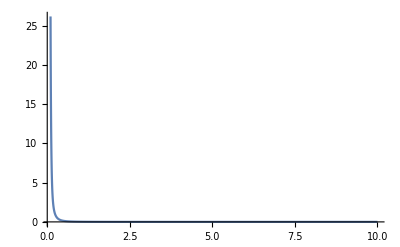

```mathematica
ProcaFieldFKKS = FKKS/.ApplySolution[AllSolutions[[1]]];
(ProcaFieldFKKS[{1, sphericalchart}]//PrepareArguments)/.θ->π/2/.t->0/.ϕ->0;
Plot[%//Abs, {r,0.1, 10}, PlotRange->All]
```

```mathematica
(Cd[{μ, sphericalchart}]@FKKS[{ν, sphericalchart}])//FromBasisExpand
```

(ⅇ^(-ⅈ ω t+ⅈ m ϕ) λ 1 1 (ⅈ m ((∂/(∂ϕ) | μ
  Csc[θ]^4 (a^2 (1[θ])^2-2 M r+r^2))/(a^4 Cot[θ]^2+2 a^2 M r-2 3 r+1+1-2 M 1^2 r^3+Csc[θ]^2 r^4)-(2 3 r)/1)-ⅈ 1 (-1/1+1)) (-r (-a m+a^2 ω+ω r^2) R[r]+λ (a^2+r (-2 M+r)) R'[r]))/((λ^2+r^2) (a^2 Cos[θ]^2+r^2))+6
 |  |  |  |